```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

D:\monitorParticle

```mathematica
SetDirectory["D:\\newLight3\\"]
```

D:\newLight3

```mathematica
GetOrg[orgNo_]:=Module[{path1,path2,birth,death},
path1 = StringForm["organisms\\org``.json",orgNo]//ToString;
path2 = StringForm["orgDeaths\\org``.json",orgNo]//ToString;
birth=Import[path1];
death=Import[path2];
{("step"/.death)-("step"/.birth),"cause"/.death}
]
```

```mathematica
deadOrganisms=
StringCases[
FileNames["*","orgDeaths"],
"orgDeaths\\org"~~i:DigitCharacter..~~".json"-> i
]//Flatten;
deadOrganisms//Length
```

631633

```mathematica
{ages,deathCauses}=Transpose[ParallelMap[GetOrg,deadOrganisms]];
```

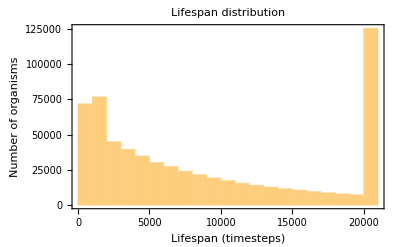

```mathematica
Histogram[ages, Frame->{{True,False},{True,False}},FrameLabel->{"Lifespan (timesteps)","Number of organisms"},PlotLabel->"Lifespan distribution"]
```

```mathematica
tally
```

{{age,125321},{disintegration,506312}}

```mathematica
tally=Tally[deathCauses];
{labels,amounts}=Transpose[tally];
PieChart[
amounts, 
ChartLabels->Placed[
{labels,N[Quantity[(100#)/Total[amounts],"Percent"],3]&/@amounts},
{"RadialCenter","RadialCallout"}],
ImageSize->250,
PlotLabel->"Death cause distribution"
]
```

-Graphics-